## 原子体系

## 二能级

### 薛定谔方程

#### 精确数值解

i ℏ ∂/(∂t)ψ = H ψ
其中H=ℏ(0 | Ωcos(ωt)
Ωcos(ωt) | ω_0), ψ=(c_1
c_2)
所以：

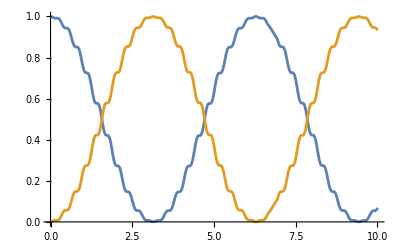

```mathematica
Clear["Global`*"]
ω0=10;
Ω=1;
ω=10;
s=NDSolve[{c1'[t]==-I Ω*Cos[ω*t]*c2[t],
c2'[t]==-I ω0 c2[t]-I Ω*Cos[ω*t]*c1[t],

c1[0]==1,c2[0]==0},{c1,c2},{t,0,30}];
Plot[{Evaluate[Abs[c1[t]]^2/.s],Evaluate[Abs[c2[t]]^2/.s]},{t,0,10},PlotRange->All]
```

#### 旋转波近似

```mathematica
Clear["Global`*"]
H=({{0, Ω/2}, {Ω/2, Δ}});
Eigensystem[H]
```

{{1/2 (Δ-√(Δ^2+Ω^2)),1/2 (Δ+√(Δ^2+Ω^2))},{{-(Δ+√(Δ^2+Ω^2))/Ω,1},{-(Δ-√(Δ^2+Ω^2))/Ω,1}}}

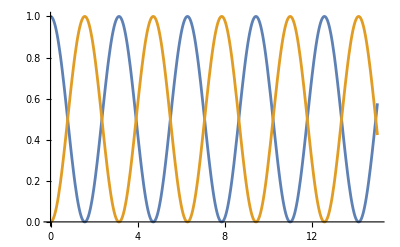

```mathematica
Clear["Global`*"]
Δ=0;
Ω=1;

s=DSolve[{c1'[t]==-I Ω c2[t],
c2'[t]==-I Δ c2[t]-I Ω**c1[t],

c1[0]==1,c2[0]==0},{c1[t],c2[t]},t];
Evaluate[c1[t]/.s];
Evaluate[c2[t]/.s];
Plot[{Evaluate[Abs[c1[t]]^2/.s],Evaluate[Abs[c2[t]]^2/.s]},{t,0,15},PlotRange->All]
```

如果考虑光场相位，Ωexp(ωt+iϕ)，旋波近似后为Ωexp(iϕ)
先看ϕ=0,但原子处于叠加态(0+i1)/√2

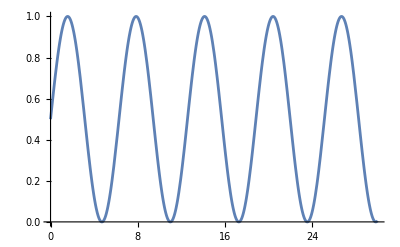

```mathematica
Clear["Global`*"]
Δ=0;
Ω=1;
s=NDSolve[{c1'[t]==-I Ω/2 c2[t],
c2'[t]==I Δ c2[t]-I (Ω*)/2*c1[t],
c1[0]==1/(√2),c2[0]==I/(√2)},{c1,c2},{t,0,30}];
Plot[{Evaluate[Abs[c1[t]]^2/.s]},{t,0,30},PlotRange->{0,1}]
```

若原子处于叠加态(0+1)/√2

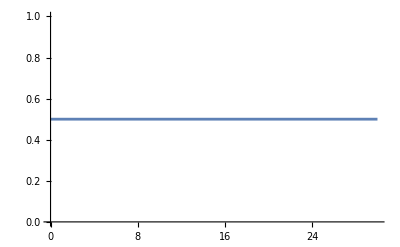

```mathematica
Clear["Global`*"]
Δ=0;
Ω=1;
s=NDSolve[{c1'[t]==-I Ω/2 c2[t],
c2'[t]==I Δ c2[t]-I (Ω*)/2*c1[t],
c1[0]==1/(√2),c2[0]==1/(√2)},{c1,c2},{t,0,30}];
Plot[{Evaluate[Abs[c1[t]]^2/.s]},{t,0,30},PlotRange->{0,1}]
```

这说明相位很重要，但这个相位其实是跟光的相位来配合的。
比如，同样原子处于叠加态(0+1)/√2，但光的初始相位为ϕ0 = π/2

```mathematica
Clear["Global`*"]
Δ=0;
Ω=1*Exp[I*π/2];
s=NDSolve[{c1'[t]==-I Ω/2 c2[t],
c2'[t]==I Δ c2[t]-I (Ω*)/2*c1[t],
c1[0]==1/(√2),c2[0]==1/(√2)},{c1,c2},{t,0,30}];
Plot[{Evaluate[Abs[c1[t]]^2/.s]},{t,0,30},PlotRange->{0,1}]
```

-Graphics-

光的初始相位改为ϕ0 = -π/2

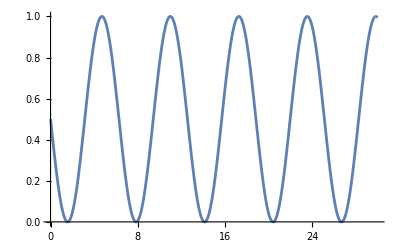

```mathematica
Clear["Global`*"]
Δ=0;
Ω=1*Exp[-I*π/2];
s=NDSolve[{c1'[t]==-I Ω/2 c2[t],
c2'[t]==I Δ c2[t]-I (Ω*)/2*c1[t],
c1[0]==1/(√2),c2[0]==1/(√2)},{c1,c2},{t,0,30}];
Plot[{Evaluate[Abs[c1[t]]^2/.s]},{t,0,30},PlotRange->{0,1}]
```

这说明，在Δ = 0时，在光的参考系中，原子态的演化完全取决于光的强度。若光强为0，即Ω = 0，则原子不会演化。其实原子的演化速度一直是exp(iω_0t）,这是因为Δ = 0时，光的演化速度也是exp(iω_0t），所以旋波近似后原子就不再演化。
但如果Δ ≠ 0，原子与光的演化不同步，这时在光的坐标系下，原子的演化速度为exp(iΔt）。

ϕ0 =0 ， 原子处于叠加态(0+1)/√2时，即使有光原子也完全不演化，这可以用block球来解释。
-Graphics-Δ = 0，Ω ≠  0时，矢量的旋转是以yz为平面，沿x轴旋转。但如果矢量的初始状态平行x轴，则矢量将不再旋转。

-Graphics-当矢量旋转至xy平面时，让Δ ≠ 0，Ω =  0时，这时矢量的旋转是以xy为平面，沿z轴旋转。

### 绝热转移

-Graphics-

转移过程中原子所在的状态能量从零降低到-Δ，这是由于旋转坐标系造成的。实际原子是从能量为零的g态变成了能量为ω0的e态。

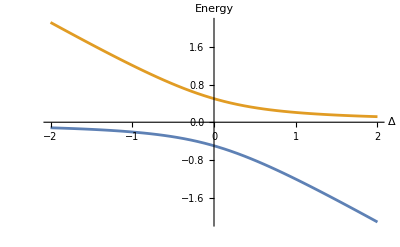

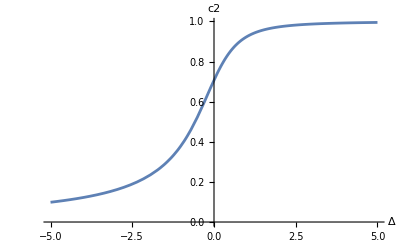

```mathematica
Clear["Global`*"]
Ω=1;
H=({{0, Ω/2}, {Ω/2, -Δ}});
e=Eigenvalues[H];
E1=e[[1]];
E2=e[[2]];

Plot[e,{Δ,-2,2},AxesLabel->{Δ,Energy}]
ϕ=Eigenvectors[H];
c11=ϕ[[1]][[1]]/√((ϕ[[1]][[1]])^2+(ϕ[[1]][[2]])^2);
c12=ϕ[[1]][[2]]/√((ϕ[[1]][[1]])^2+(ϕ[[1]][[2]])^2);
Plot[{c12},{Δ,-5,5},AxesLabel->{Δ,c2}]
```

从原子态ϕ=c1g+c2e中e的占比(c2)中可以看出，c2的占比越来越大，所以实际原子态的能量逐渐增大。c2的曲线与实际能量的曲线完全相同。

### 主方程(密度矩阵)

i ℏ ∂/(∂t)ρ = [H,ρ]
[H,ρ] = (0 | Ωe^iωt
Ωe^-iωt | ω_0)(ρ_11 | ρ_12
ρ_21 | ρ_22) - (ρ_11 | ρ_12
ρ_21 | ρ_22) (0 | Ωe^iωt
Ωe^-iωt | ω_0)
	 =(Ω(e^iωt ρ_21-e^-iωt ρ_12) | A
B | Ω(e^-iωt ρ_12-e^iωt ρ_21))
其中，A = -ω_0 ρ_12+Ω(e^iωt ρ_22-e^-iωt ρ_11)  ，B= ω_0 ρ_21-Ω(e^iωt ρ_22-e^-iωt ρ_11)
旋波近似后
[H,ρ] = (Ω(ρ_21-ρ_12) | A
B | Ω(ρ_12-ρ_21))
其中，A = Δρ_12+Ω(ρ_22-ρ_11)  ，B = -Δρ_21-Ω(ρ_22-ρ_11)
——《Quantum and Atom Optics》 Daniel Adam Steck     P169

```mathematica
Clear["Global`*"]
ρ=({{ρ11, ρ12}, {ρ21, ρ22}});
H=({{0, Ω}, {Ω, Δ}});
MatrixForm[H.ρ-ρ.H]
```

(-ρ12 Ω+ρ21 Ω | -Δ ρ12-ρ11 Ω+ρ22 Ω
Δ ρ21+ρ11 Ω-ρ22 Ω | ρ12 Ω-ρ21 Ω)

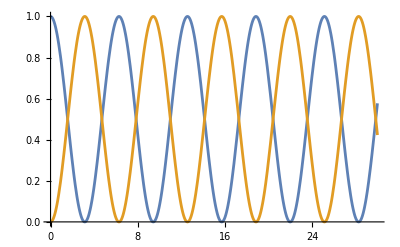

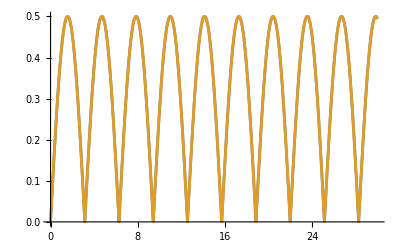

```mathematica
Clear["Global`*"]
Δ=0;
Ω=1;

s=NDSolve[{ρ11'[t]==-I Ω/2(ρ21[t]-ρ12[t]),
ρ12'[t]==-I Δ*ρ12[t]-I Ω/2(ρ22[t]-ρ11[t]),
ρ21'[t]==I Δ*ρ21[t]+I Ω/2(ρ22[t]-ρ11[t]),
ρ22'[t]==I Ω/2(ρ21[t]-ρ12[t]),

ρ11[0]==1,ρ12[0]==0,ρ21[0]==0,ρ22[0]==0},{ρ11,ρ12,ρ21,ρ22},{t,0,30}];
Plot[{Evaluate[Abs[ρ11[t]]/.s],Evaluate[Abs[ρ22[t]]/.s]},{t,0,30},PlotRange->All]
Plot[{Evaluate[Abs[ρ12[t]]/.s],Evaluate[Abs[ρ21[t]]/.s]},{t,0,30},PlotRange->All]
```

这样方便引入耗散项

∂/(∂t) ρ_22= - Γρ_22
∂/(∂t) ρ_11=  Γρ_22
∂/(∂t) ρ_12=  -γρ_12
∂/(∂t) ρ_21=  -γρ_21
通常γ > Γ/2 ,即 γ = Γ/2 + γ_c
i ℏ ∂/(∂t)ρ =  (Ω(ρ_21-ρ_12)+iΓρ_22 | A-iγρ_12
B-iγρ_21 | Ω(ρ_12-ρ_21)-iΓρ_22)
其中，A = Δρ_12+Ω(ρ_22-ρ_11)  ，B = -Δρ_21-Ω(ρ_22-ρ_11)

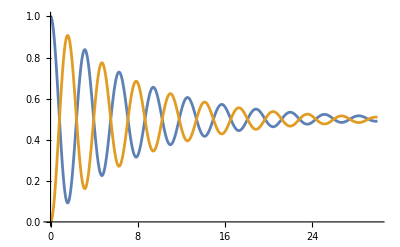

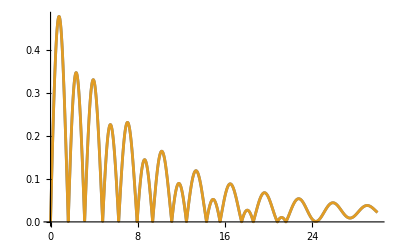

```mathematica
Clear["Global`*"]
Δ=0;
Ω=2;
Γ=0.1;
γ=Γ/2+0.1;
s=NDSolve[{ρ11'[t]==-I Ω/2(ρ21[t]-ρ12[t])+Γ*ρ22[t],
ρ12'[t]==-I Δ*ρ12[t]-I Ω/2(ρ22[t]-ρ11[t])-γ*ρ12[t],
ρ21'[t]==I Δ*ρ21[t]+I Ω/2(ρ22[t]-ρ11[t])-γ*ρ21[t],
ρ22'[t]==I Ω/2(ρ21[t]-ρ12[t])-Γ*ρ22[t],

ρ11[0]==1,ρ12[0]==0,ρ21[0]==0,ρ22[0]==0},{ρ11,ρ12,ρ21,ρ22},{t,0,30}];
Plot[{Evaluate[ρ11[t]/.s],Evaluate[ρ22[t]/.s]},{t,0,30},PlotRange->All]
Plot[{Evaluate[Abs[ρ12[t]]/.s],Evaluate[Abs[ρ21[t]]/.s]},{t,0,30},PlotRange->All]
```

验证另一种编程思路，同时也是另一种理论
《开放系统的 Lindblad 方程》
∂/(∂t)ρ = -i[H,ρ] + ∑_k ( L_k ρ L_k†-1/2{L_k†L_k ,ρ} )

master equation for the density operator
∂/(∂t)ρ = -i[H,ρ] + Γ𝒟[σ]ρ + γ_c 𝒟[σ_z]ρ
其中,Lindbladc超算符：𝒟[σ]ρ  = σρσ† + 1/2(σ†σρ + ρσ†σ)
σ为降算符，但书中对密度矩阵的定义为(ρee | ρeg
ρge | ρgg)
——《Quantum and Atom Optics》 Daniel Adam Steck     P177

```mathematica
Clear["Global`*"]
ρ=({{ρ11[t], ρ12[t]}, {ρ21[t], ρ22[t]}});H=({{0, Ω/2}, {Ω/2, Δ}});Mγ=({{Γ*ρ22[t], -γ*ρ12[t]}, {-γ*ρ21[t], -Γ*ρ22[t]}});
MatrixForm[-I(H.ρ-ρ.H)+Mγ]
```

(-ⅈ (-1/2 Ω ρ12[t]+1/2 Ω ρ21[t])+Γ ρ22[t] | -γ ρ12[t]-ⅈ (-1/2 Ω ρ11[t]-Δ ρ12[t]+1/2 Ω ρ22[t])
-γ ρ21[t]-ⅈ (1/2 Ω ρ11[t]+Δ ρ21[t]-1/2 Ω ρ22[t]) | -ⅈ (1/2 Ω ρ12[t]-1/2 Ω ρ21[t])-Γ ρ22[t])

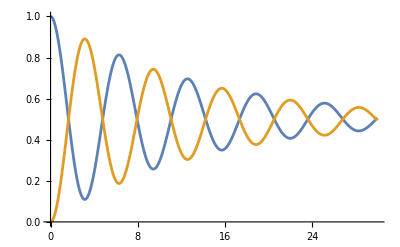

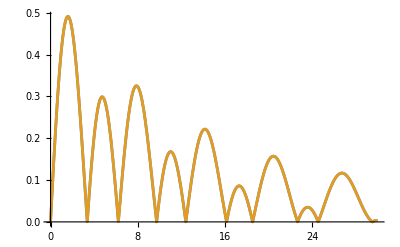

```mathematica
Clear["Global`*"]
Δ=0;
Ω=1;
Γ=0.1;
ρ=({{ρ11[t], ρ12[t]}, {ρ21[t], ρ22[t]}});H=({{0, Ω/2}, {Ω/2, Δ}});
ℒ12=({{0, 1}, {0, 0}});
Dρ[ℒ_]=ℒ.ρ.ℒ†-1/2(ℒ†.ℒ.ρ+ρ.ℒ†.ℒ);
MΓ=Γ*Dρ[ℒ12];
ρt=({{ρ11'[t], ρ12'[t]}, {ρ21'[t], ρ22'[t]}});
ρ0=({{ρ11[0], ρ12[0]}, {ρ21[0], ρ22[0]}});c0=({{1, 0}, {0, 0}});
s=NDSolve[{ρt==-I(H.ρ-ρ.H)+MΓ,ρ0== c0},{ρ11,ρ12,ρ21,ρ22},{t,0,30}];
Plot[{Evaluate[ρ11[t]/.s],Evaluate[ρ22[t]/.s]},{t,0,30},PlotRange->All]
Plot[{Evaluate[Abs[ρ12[t]]/.s],Evaluate[Abs[ρ21[t]]/.s]},{t,0,30},PlotRange->All]
```

### 海森堡方程

与密度矩阵的演化十分类似,但差个负号，所以一般把对易关系换一下
i ℏ ∂/(∂t)<σ> = <[σ，H]>

这与密度矩阵的演化十分类似

```mathematica
Clear["Global`*"]
σ=({{0, 1}, {0, 0}});
σz=({{1, 0}, {0, -1}});
ϕ=({{a}, {b}});
MatrixForm[ϕ†.σ.ϕ]
MatrixForm[σ.σ†-σ†.σ];
MatrixForm[σz.σ];
MatrixForm[ϕ†.σz.ϕ]
```

(b Conjugate[a])

(a Conjugate[a]-b Conjugate[b])

而 ρ12 = ，所以σ的期望值的演化就完全等价与ρ12的演化。

### Shift and Scatter

#### Ac Stark Shift

```mathematica
Clear["Global`*"]
H=({{-Δ/2, Ω/2}, {Ω/2, Δ/2}});
e=Eigenvalues[H];
E1=e[[1]];
E2=e[[2]];
Series[E1,{Ω,0,3}];
Print["基态能量E1= ",E1,", ","小量展开E1= ",-Ω^2/(4 Δ)]
```

基态能量E1= -1/2 √(Δ^2+Ω^2), 小量展开E1= -Ω^2/(4 Δ)

#### Scatter

```mathematica
Clear["Global`*"]
H=({{0, Ω/2}, {Ω/2, Δ}});
e=Eigenvalues[H];
E1=e[[1]];
E2=e[[2]];
Series[E1,{Ω,0,3}];
Print["基态能量E1= ",E1,", ","小量展开E1= ",-Ω^2/(4 Δ)]
```

基态能量E1= 1/2 (Δ-√(Δ^2+Ω^2)), 小量展开E1= -Ω^2/(4 Δ)

基态能量为0，激发态为Δ，所以新的本征态能量为-Ω^2/(4 Δ)意味着激发态的占比为
，即 
新本征态的散射速率：

但实际考虑自发辐射后，哈密顿量会变成

H=(0 | Ω/2
Ω/2 | Δ+I Γ/2)
（参考随机波函数法（Stochastic Wavefunction））
这时等效Δ'=Δ+I Γ/2 不可能取到零。所以不用担心散射速率在Δ=0时发散。
Δ=0时,，这在Ω<<Γ时已经是真实情况了。
但，为了满足这一条件，还需要再进行修正。

### 随机波函数法（Stochastic Wavefunction）

构建非厄密哈密顿量

```mathematica
Clear["Global`*"]
H=({{0, Ω/2}, {Ω/2, Δ+I Γ/2}});ρ=({{ρ11[t], ρ12[t]}, {ρ21[t], ρ22[t]}});
MatrixForm[-I(H.ρ-ρ.H)]
```

(-ⅈ (-1/2 Ω ρ12[t]+1/2 Ω ρ21[t]) | -ⅈ (-1/2 Ω ρ11[t]-((ⅈ Γ)/2+Δ) ρ12[t]+1/2 Ω ρ22[t])
-ⅈ (1/2 Ω ρ11[t]+((ⅈ Γ)/2+Δ) ρ21[t]-1/2 Ω ρ22[t]) | -ⅈ (1/2 Ω ρ12[t]-1/2 Ω ρ21[t]))

与原来的密度矩阵演化相比，只差了对角项的decay部分，即quantum jump。缺的部分无法通过薛定谔方程弥补，只能在解薛定谔方程时加入随机jump项，用蒙特卡洛求解。
—— 《Lukin note 》Chapter 6   Stochastic Wavefunctions

对角化哈密顿量，得到有自发辐射时的AC  stark  shift

1/2 ((0.+0.1 ⅈ)+Δ-√((0.99+0. ⅈ)+(0.+0.2 ⅈ) Δ+1. Δ^2))

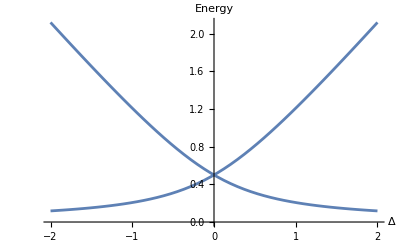

```mathematica
Clear["Global`*"]
Ω=1;Γ=0.2;
H=({{0, Ω/2}, {Ω/2, Δ+I Γ/2}});
e=Eigenvalues[H];
E1=e[[1]]
E2=e[[2]];

Plot[Abs[e],{Δ,-2,2},AxesLabel->{Δ,Energy}]
ϕ=Eigenvectors[H];
c11=ϕ[[1]][[1]]/√((ϕ[[1]][[1]])^2+(ϕ[[1]][[2]])^2);
c12=ϕ[[1]][[2]]/√((ϕ[[1]][[1]])^2+(ϕ[[1]][[2]])^2);
```

### Quantum Zeno effect

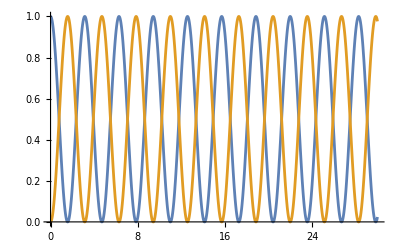

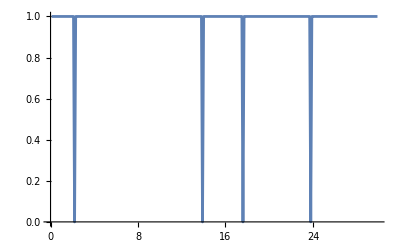

```mathematica
Clear["Global`*"]
Δ=0;
Ω=2;
Γ=0;
γ=Γ/2+0;


s=NDSolve[{ρ11'[t]==-I Ω/2(ρ21[t]-ρ12[t])+Γ*ρ22[t],
ρ12'[t]==-I Δ*ρ12[t]-I Ω/2(ρ22[t]-ρ11[t])-γ*ρ12[t],
ρ21'[t]==I Δ*ρ21[t]+I Ω/2(ρ22[t]-ρ11[t])-γ*ρ21[t],
ρ22'[t]==I Ω/2(ρ21[t]-ρ12[t])-Γ*ρ22[t],

ρ11[0]==1,ρ12[0]==0,ρ21[0]==0,ρ22[0]==0},{ρ11,ρ12,ρ21,ρ22},{t,0,30}];
dt=0.1;
meanN=Round[30/dt];
tou=RandomReal[1,meanN];
P2[t_]=Evaluate[ρ22[t]/.s];
thr=First[Abs[P2[dt]]];
data={};t=0;
For[k1=1,k1<meanN,k1=k1+1,
t=t+dt;
If[tou[[k1]]<thr,AppendTo[data,{t,0}],AppendTo[data,{t,1}]];
]

Plot[{Evaluate[ρ11[t]/.s],Evaluate[ρ22[t]/.s]},{t,0,30},PlotRange->All]
ListPlot[data,Joined->True]
Plot[{Evaluate[Abs[ρ12[t]]/.s],Evaluate[Abs[ρ21[t]]/.s]},{t,0,30},PlotRange->All];
```

### 自旋波

自旋波即两个自旋能级的密度矩阵非对角元，ρ12 = c1·c2*
其ρ12 通常是复数

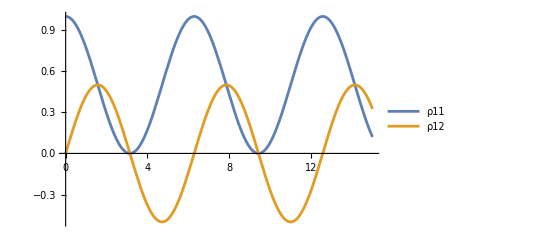

```mathematica
Clear["Global`*"]
Δ=0;
Ω=1;

s=DSolve[{c1'[t]==-I Ω/2 c2[t],
c2'[t]==-I Δ c2[t]-I Ω/2*c1[t],

c1[0]==1,c2[0]==0},{c1[t],c2[t]},t];
Plot[{Evaluate[Re[c1[t]*c1[t]*]/.s],Evaluate[Im[c1[t]*c2[t]*]/.s]},{t,0,15},PlotRange->All,PlotLegends->{"ρ11","ρ12"}]
```

## 三能级

### 薛定谔方程

#### 含时薛定谔方程

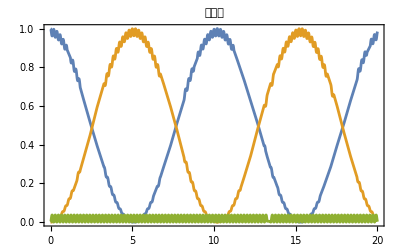

```mathematica
Ω1=2*π*1;Ω2=2*π*1;
δ=0;Δ=2*π*5;

ϕ=({{c1[t]}, {c2[t]}, {c3[t]}});
ϕp=({{c1'[t]}, {c2'[t]}, {c3'[t]}});
Δ13=Δ;
Δ23=Δ-δ;
H=({{0, 0, Ω1/2}, {0, Δ13-Δ23, Ω2/2}, {Ω1/2, Ω2/2, Δ13}});
s=NDSolve[{ϕp==-I*H.ϕ,({{c1[0]}, {c2[0]}, {c3[0]}})== ({{1}, {0}, {0}})},{c1,c2,c3},{t,0,20}];

Plot[{Abs[Evaluate[c1[t]/.s]]^2,Abs[Evaluate[c2[t]/.s]]^2,Abs[Evaluate[c3[t]/.s]]^2},{t,0,20},PlotRange->All,Frame->True,PlotLabel->"占居数"]
```

### 密度矩阵

#### 稳态

Master equation for the density operator
∂/(∂t)ρ = -i[H,ρ] + Γ𝒟[σ]ρ + γ_c 𝒟[σ_z]ρ
其中,Lindbladc超算符：𝒟[σ]ρ  = σρσ† - 1/2(σ†σρ + ρσ†σ)
——《Quantum and Atom Optics》 Daniel Adam Steck     P177

i ℏ ∂/(∂t)ρ = [H,ρ]
求稳态解的话，-i[H,ρ] = 0

```mathematica
Clear["Global`*"]

ρ=({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}});H=({{0, 0, Ω1}, {0, δ, Ω2}, {Ω1, Ω2, Δ}});
ℒ13=({{0, 0, 1}, {0, 0, 0}, {0, 0, 0}});ℒ23=({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}});ℒz=({{1, 0, 0}, {0, -1, 0}, {0, 0, 0}});

Dρ[ℒ_]=ℒ.ρ.ℒ†-1/2(ℒ†.ℒ.ρ+ρ.ℒ†.ℒ);
MΓ=(1Γ)/3*Dρ[ℒ13]+(2Γ)/3*Dρ[ℒ23];(*Γ的分配取决于CG系数*)
MΓ=Γ*Dρ[ℒ13];(*Γ的分配取决于CG系数*)
Mγ=γ*Dρ[ℒz];
MatrixForm[MΓ]
```

(Γ ρ33 | 0 | -(Γ ρ13)/2
0 | 0 | -(Γ ρ23)/2
-(Γ ρ31)/2 | -(Γ ρ32)/2 | -Γ ρ33)

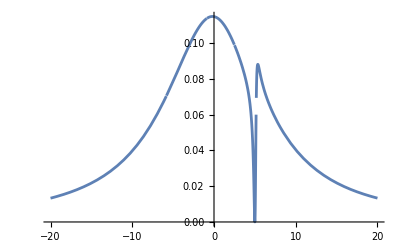

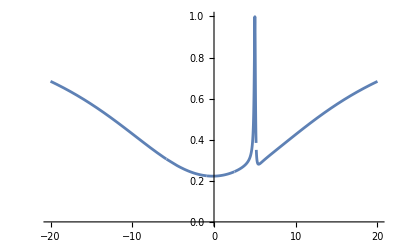

```mathematica
Clear["Global`*"]
Γ=6;

Ω1=1;
Ω2=2;
γ=0;

Δ13=Δ;
Δ23=5;
ρ33=1-ρ11-ρ22;
ρ=({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}});
H=({{0, 0, Ω1/2}, {0, Δ13-Δ23, Ω2/2}, {Ω1/2, Ω2/2, Δ13}});
ℒ13=({{0, 0, 1}, {0, 0, 0}, {0, 0, 0}});ℒ23=({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}});ℒz=({{1, 0, 0}, {0, -1, 0}, {0, 0, 0}});
Dρ[ℒ_]=ℒ.ρ.ℒ†-1/2(ℒ†.ℒ.ρ+ρ.ℒ†.ℒ);
MΓ=(3Γ)/3*Dρ[ℒ13]+(3Γ)/3*Dρ[ℒ23];(*Γ的分配取决于CG系数*)
Mγ=γ*Dρ[ℒz];
s=NSolve[{({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})==-I(H.ρ-ρ.H)+MΓ+Mγ},{ρ11,ρ12,ρ13,ρ21,ρ22,ρ23,ρ31,ρ32}];
σ11[Δ_]=Re[ρ11]/.s[[1]];
σ22[Δ_]=Re[ρ22]/.s[[1]];
σ12[Δ_]=Im[ρ12]/.s[[1]];
σ13[Δ_]=ρ13/.s[[1]];
σ23[Δ_]=Im[ρ23]/.s[[1]];
σ33[Δ_]=1-σ11[Δ]-σ22[Δ];

Plot[{Im[σ13[Δ]]/(Ω1/2)},{Δ,-20,20},PlotRange->All]
κ=0.037;g=0.6;as=Ω1/g;
Trans[Δ_]=Abs[1/(I(0+g σ13[Δ]/as)/(κ/2)-1)]^2;
Plot[Trans[Δ],{Δ,-20,20},PlotRange->{0,1}]
```

#### 弱激发近似

近似原则：对角项不能删？为什么
非对角项中的ρ23和ρ33都可以删掉

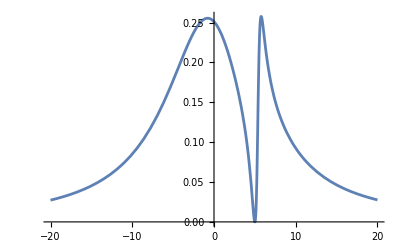

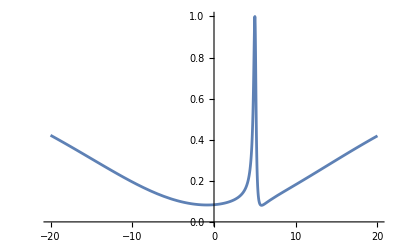

```mathematica
Clear["Global`*"]
Γ=6;

Ω1=1;
Ω2=2;

Δ13=Δ;
Δ23=5;
δ=Δ13-Δ23;

ρ33=1-ρ11-ρ22;
ρ=({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}});
H=({{0, 0, Ω1/2}, {0, δ, Ω2/2}, {Ω1/2, Ω2/2, Δ13}});
ℒ13=({{0, 0, 1}, {0, 0, 0}, {0, 0, 0}});ℒ23=({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}});ℒz=({{1, 0, 0}, {0, -1, 0}, {0, 0, 0}});
Dρ[ℒ_]=ℒ.ρ.ℒ†-1/2(ℒ†.ℒ.ρ+ρ.ℒ†.ℒ);
MΓ=(3Γ)/3*Dρ[ℒ13]+(3Γ)/3*Dρ[ℒ23];(*Γ的分配取决于CG系数*)

(*s=NSolve[{({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})==({{-ⅈ (-ρ13 Ω1+ρ31 Ω1), -ⅈ (-δ ρ12+ρ32 Ω1-ρ13 Ω2), -ⅈ (-Δ ρ13-ρ11 Ω1+ρ33 Ω1-ρ12 Ω2)}, {-ⅈ (δ ρ21-ρ23 Ω1+ρ31 Ω2), -ⅈ (-ρ23 Ω2+ρ32 Ω2), -ⅈ (δ ρ23-Δ ρ23-ρ21 Ω1-ρ22 Ω2+ρ33 Ω2)}, {-ⅈ (Δ ρ31+ρ11 Ω1-ρ33 Ω1+ρ21 Ω2), -ⅈ (-δ ρ32+Δ ρ32+ρ12 Ω1+ρ22 Ω2-ρ33 Ω2), -ⅈ (ρ13 Ω1-ρ31 Ω1+ρ23 Ω2-ρ32 Ω2)}})+MΓ},{ρ11,ρ12,ρ13,ρ21,ρ22,ρ23,ρ31,ρ32}];*)
s=NSolve[{({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})==({{-ⅈ (-ρ13 Ω1+ρ31 Ω1), -ⅈ (-δ ρ12-ρ13 Ω2), -ⅈ (-Δ ρ13-ρ11 Ω1-ρ12 Ω2)}, {-ⅈ (δ ρ21+ρ31 Ω2), -ⅈ (-ρ23 Ω2+ρ32 Ω2), -ⅈ (-ρ21 Ω1-ρ22 Ω2)}, {-ⅈ (Δ ρ31+ρ11 Ω1+ρ21 Ω2), -ⅈ (ρ12 Ω1+ρ22 Ω2), -ⅈ (ρ13 Ω1-ρ31 Ω1+ρ23 Ω2-ρ32 Ω2)}})+MΓ},{ρ11,ρ12,ρ13,ρ21,ρ22,ρ23,ρ31,ρ32}];
σ13[Δ_]=ρ13/.s[[1]];


Plot[{Im[σ13[Δ]]/(Ω1/2)},{Δ,-20,20},PlotRange->All]
κ=0.037;g=0.6;as=Ω1/g;
Trans[Δ_]=Abs[1/(I(0+g σ13[Δ]/as)/(κ/2)-1)]^2;
Plot[Trans[Δ],{Δ,-20,20},PlotRange->{0,1}]
```

#### 含时演化

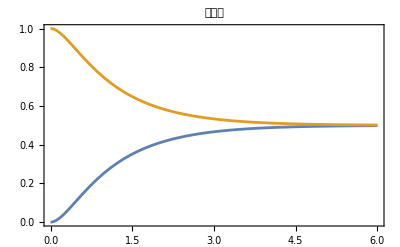

```mathematica
Clear["Global`*"]
κ=10;g=1;
Ω1=0;
Δ13=0;Δ23=0;


ρ33[t]=1-ρ11[t]-ρ22[t];
ρ=({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
ℒ13=({{0, 0, 1}, {0, 0, 0}, {0, 0, 0}});ℒ23=({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}});ℒz=({{1, 0, 0}, {0, -1, 0}, {0, 0, 0}});
Dρ[ℒ_]=ℒ.ρ.ℒ†-1/2(ℒ†.ℒ.ρ+ρ.ℒ†.ℒ);
MΓ=κ*Dρ[ℒz];(*Γ的分配取决于CG系数*)


H=({{0, 0, Ω1/2}, {0, Δ13-Δ23, g}, {Ω1/2, g, Δ13}});
s=NDSolve[{({{ρ11'[t], ρ12'[t], ρ13'[t]}, {ρ21'[t], ρ22'[t], ρ23'[t]}, {ρ31'[t], ρ32'[t], ρ33'[t]}})==-I(H.ρ-ρ.H)+MΓ,({{ρ11[0], ρ12[0], ρ13[0]}, {ρ21[0], ρ22[0], ρ23[0]}, {ρ31[0], ρ32[0], ρ33[0]}})== ({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}})},{ρ11,ρ12,ρ13,ρ21,ρ22,ρ23,ρ31,ρ32},{t,0,10}];

Plot[{Evaluate[ρ11[t]/.s]+Evaluate[ρ22[t]/.s],Evaluate[ρ33[t]/.s]},{t,0,6},PlotRange->All,Frame->True,PlotLabel->"占居数"]
```

### EIT

《AOM》-- Lukin P85

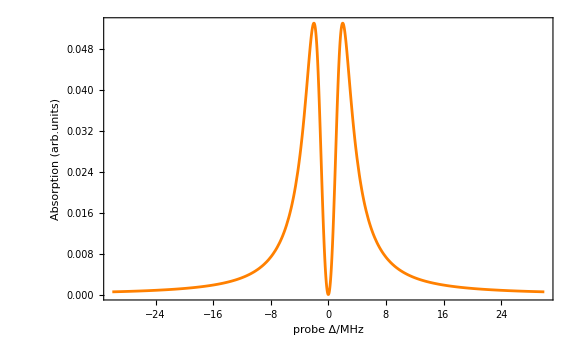

```mathematica
Clear["Global`*"]
Γ13=2*π*(3-I*Δ13);
Γ12=2*π*(0-I*(Δ13-Δ23));
χ[Δ13_,Δ23_,Ω23_]=I/Γ13*Γ12/(Γ12+Ω23^2/Γ13);
Plot[Im[χ[Δ13,0,2*π*2]],{Δ13,-30,30},PlotStyle->Orange,Frame->True,Axes->False,FrameLabel->{{Style["Absorption (arb.units)",20,Black],None},{Style["probe Δ/MHz",20,Black],None}},FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->20,ImageSize->Large,PlotRange->All]
```

EIT附近（Δ~0）,EIT窗口

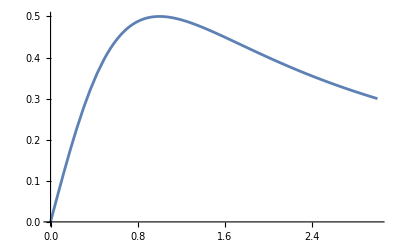

### STIRAP

#### STIRAP原理

{{0,-√(1+Ω1^2),√(1+Ω1^2)},{{-1/Ω1,1,0},{-Ω1/(√(1+Ω1^2)),-1/(√(1+Ω1^2)),1},{Ω1/(√(1+Ω1^2)),1/(√(1+Ω1^2)),1}}}

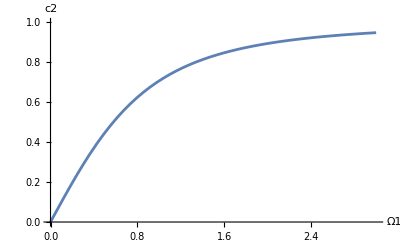

```mathematica
Clear["Global`*"]
Ω2=1;δ=0;Δ=0;
H=({{0, 0, Ω1}, {0, δ, Ω2}, {Ω1, Ω2, Δ}});
e=Eigensystem[H]
c12=e[[2]][[1]][[2]]/√((e[[2]][[1]][[1]])^2+(e[[2]][[1]][[2]])^2+(e[[2]][[1]][[3]])^2);
Plot[{c12},{Ω1,0,3},AxesLabel->{Ω1,c2},PlotRange->{0,1}]
```

从薛定谔方程上看,一开始只开Ω2，原子在g态上保持不变。

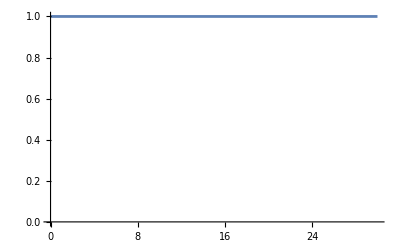

```mathematica
Clear["Global`*"]
Ω1=0;Ω2=1;δ=0;Δ=0;
s=NDSolve[{c1'[t]==-I Ω1*c3[t],
c2'[t]==-I δ c2[t]-I Ω2*c3[t],
c3'[t]==-I Ω1**c1[t]-I Ω2**c2[t]-I Δ*c3[t],
c1[0]==1,c2[0]==0,c3[0]==0},{c1,c2,c3},{t,0,30}];
Plot[{Evaluate[Abs[c1[t]]^2/.s]},{t,0,30},PlotRange->{0,1}]
```

然后让Ω1  =Ω2，如果原子还在 g态上，将开始振荡。

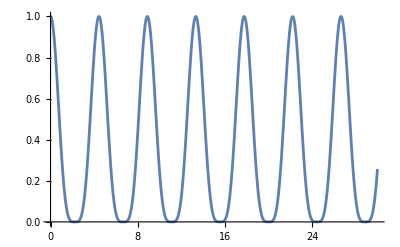

```mathematica
Clear["Global`*"]
Ω1=1;Ω2=1;δ=0;Δ=0;
s=NDSolve[{c1'[t]==-I Ω1*c3[t],
c2'[t]==-I δ c2[t]-I Ω2*c3[t],
c3'[t]==-I Ω1**c1[t]-I Ω2**c2[t]-I Δ*c3[t],
c1[0]==1,c2[0]==0,c3[0]==0},{c1,c2,c3},{t,0,30}];
Plot[{Evaluate[Abs[c1[t]]^2/.s]},{t,0,30},PlotRange->{0,1}]
```

但如果原子处在暗态D=g-s上的话，原子将保持不变。

```mathematica
Clear["Global`*"]
Ω1=1;Ω2=1;δ=0;Δ=0;
s=NDSolve[{c1'[t]==-I Ω1*c3[t],
c2'[t]==-I δ c2[t]-I Ω2*c3[t],
c3'[t]==-I Ω1**c1[t]-I Ω2**c2[t]-I Δ*c3[t],
c1[0]==1/(√2),c2[0]==-1/(√2),c3[0]==0},{c1,c2,c3},{t,0,30}];
Plot[{Evaluate[Abs[c1[t]]^2/.s]},{t,0,30},PlotRange->{0,1}]
```

-Graphics-

但如果原子处于暗态时，光的相位改变，例如Ω2 -> Ω2exp(iπ/2)

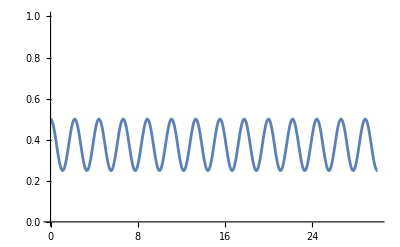

```mathematica
Clear["Global`*"]
Ω1=1;Ω2=1*Exp[I*π/2];δ=0;Δ=0;
s=NDSolve[{c1'[t]==-I Ω1*c3[t],
c2'[t]==-I δ c2[t]-I Ω2*c3[t],
c3'[t]==-I Ω1**c1[t]-I Ω2**c2[t]-I Δ*c3[t],
c1[0]==1/(√2),c2[0]==-1/(√2),c3[0]==0},{c1,c2,c3},{t,0,30}];
Plot[{Evaluate[Abs[c1[t]]^2/.s]},{t,0,30},PlotRange->{0,1}]
```

如果Ω1 -> Ω1exp (iπ/2) , Ω2 -> Ω2exp (iπ/2)

```mathematica
Clear["Global`*"]
Ω1=1*Exp[I*π/2];Ω2=1*Exp[I*π/2];δ=0;Δ=0;
s=NDSolve[{c1'[t]==-I Ω1*c3[t],
c2'[t]==-I δ c2[t]-I Ω2*c3[t],
c3'[t]==-I Ω1**c1[t]-I Ω2**c2[t]-I Δ*c3[t],
c1[0]==1/(√2),c2[0]==-1/(√2),c3[0]==0},{c1,c2,c3},{t,0,30}];
Plot[{Evaluate[Abs[c1[t]]^2/.s]},{t,0,30},PlotRange->{0,1}]
```

-Graphics-

可见，这时所谓光的相位其实是Ω1和Ω2的相位差，只要相位差不变，就不会对原子产生新的影响。

#### STIRAP含时演化

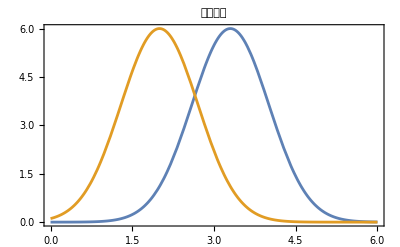

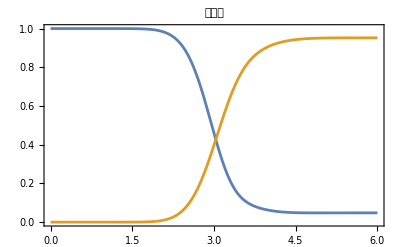

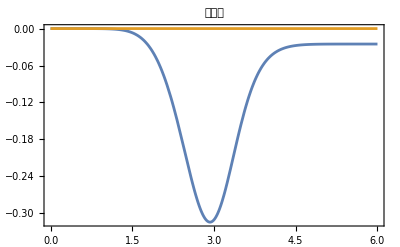

```mathematica
Clear["Global`*"]
γ=0;Γ=6;
Δ13=0;Δ23=0;
ρ33[t]=1-ρ11[t]-ρ22[t];
ρ=({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
ℒ13=({{0, 0, 1}, {0, 0, 0}, {0, 0, 0}});ℒ23=({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}});ℒz=({{1, 0, 0}, {0, -1, 0}, {0, 0, 0}});
Dρ[ℒ_]=ℒ.ρ.ℒ†-1/2(ℒ†.ℒ.ρ+ρ.ℒ†.ℒ);
MΓ=(1Γ)/3*Dρ[ℒ13]+(2Γ)/3*Dρ[ℒ23];(*Γ的分配取决于CG系数*)
Mγ=γ*Dρ[ℒz];

t0=3.3;
Ω1=6*Exp[-(2(t-t0)^2)/2];
Ω2=6*Exp[-(2(t-2)^2)/2];
H=({{0, 0, Ω1/2}, {0, Δ13-Δ23, Ω2/2}, {Ω1/2, Ω2/2, Δ13}});
s=NDSolve[{({{ρ11'[t], ρ12'[t], ρ13'[t]}, {ρ21'[t], ρ22'[t], ρ23'[t]}, {ρ31'[t], ρ32'[t], ρ33'[t]}})==-I(H.ρ-ρ.H)+MΓ+Mγ,({{ρ11[0], ρ12[0], ρ13[0]}, {ρ21[0], ρ22[0], ρ23[0]}, {ρ31[0], ρ32[0], ρ33[0]}})== ({{1, 0, 0}, {0, 0, 0}, {0, 0, 0}})},{ρ11,ρ12,ρ13,ρ21,ρ22,ρ23,ρ31,ρ32},{t,0,10}];

Plot[{Ω1,Ω2},{t,0,6},Frame->True,PlotLabel->"电场振幅"]
Plot[{Evaluate[ρ11[t]/.s],Evaluate[ρ22[t]/.s]},{t,0,6},PlotRange->All,Frame->True,PlotLabel->"占居数"]
Plot[{Evaluate[Re[ρ12[t]]/.s],Evaluate[Im[ρ12[t]]/.s]},{t,0,6},PlotRange->All,Frame->True,PlotLabel->"自旋波"]
```

求最佳时间间隔

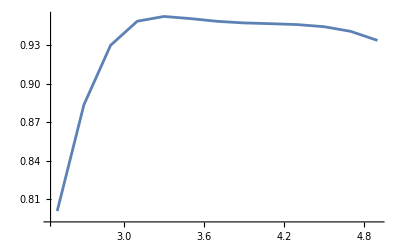

```mathematica
Clear["Global`*"]
γ=0;Γ=6;
Δ13=0;Δ23=0;
ρ33[t]=1-ρ11[t]-ρ22[t];
ρ=({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
ℒ13=({{0, 0, 1}, {0, 0, 0}, {0, 0, 0}});ℒ23=({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}});ℒz=({{1, 0, 0}, {0, -1, 0}, {0, 0, 0}});
Dρ[ℒ_]=ℒ.ρ.ℒ†-1/2(ℒ†.ℒ.ρ+ρ.ℒ†.ℒ);
MΓ=(1Γ)/3*Dρ[ℒ13]+(2Γ)/3*Dρ[ℒ23];(*Γ的分配取决于CG系数*)
Mγ=γ*Dρ[ℒz];

sList={};
For[t0=2.5,t0<5,t0=t0+0.2,
Ω1=6*Exp[-(2(t-t0)^2)/2];
Ω2=6*Exp[-(2(t-2)^2)/2];
H=({{0, 0, Ω1/2}, {0, Δ13-Δ23, Ω2/2}, {Ω1/2, Ω2/2, Δ13}});
s=NDSolve[{({{ρ11'[t], ρ12'[t], ρ13'[t]}, {ρ21'[t], ρ22'[t], ρ23'[t]}, {ρ31'[t], ρ32'[t], ρ33'[t]}})==-I(H.ρ-ρ.H)+MΓ+Mγ,({{ρ11[0], ρ12[0], ρ13[0]}, {ρ21[0], ρ22[0], ρ23[0]}, {ρ31[0], ρ32[0], ρ33[0]}})== ({{1, 0, 0}, {0, 0, 0}, {0, 0, 0}})},{ρ11,ρ12,ρ13,ρ21,ρ22,ρ23,ρ31,ρ32},{t,0,10}];
AppendTo[sList,{t0,First[ρ22[6]/.s]}]
];
ListPlot[sList,Joined->True,PlotRange->All]
(*Plot[{Ω1,Ω2},{t,0,6}]
Plot[{Evaluate[ρ11[t]/.s],Evaluate[ρ22[t]/.s]},{t,0,6},PlotRange->All]*)
(*Plot[{Evaluate[Abs[ρ12[t]]/.s],Evaluate[Abs[ρ21[t]]/.s]},{t,0,30},PlotRange->All]*)
```

## 量子比特

```mathematica
ϕ=1/2({{1}, {I}, {I}, {1}});

ρ=ϕ.ϕ†
ϕ=1/(√2)({{1}, {0}, {0}, {I}});

ϕ†.ρ.ϕ

MatrixPlot[ϕ.ϕ†];
```

{{1/4,-ⅈ/4,-ⅈ/4,1/4},{ⅈ/4,1/4,1/4,ⅈ/4},{ⅈ/4,1/4,1/4,ⅈ/4},{1/4,-ⅈ/4,-ⅈ/4,1/4}}

{{1/4}}

```mathematica
{{"受控非门（controlled not gate）", gCNOT=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}})}, {"受控相移门（controlled phase gate）", gCP=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}})}, {"加法器（自创）", gPl=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}})}, {"SWAP", gSWAP=({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}})}, {"iSWAP", giSWAP=({{1, 0, 0, 0}, {0, 0, I, 0}, {0, I, 0, 0}, {0, 0, 0, 1}})}};
ϕ=1/(√2)({{0}, {1}, {1}, {0}});
MatrixForm[giSWAP.ϕ]
```

(0
ⅈ/(√2)
ⅈ/(√2)
0)

```mathematica
U=({{1, 0}, {0, 1}});
ϕ=1/(√2)({{1}, {1}, {0}, {0}});
ϕA=({{1}, {0}});
ϕB=1/(√2)({{1}, {1}});
ϕ1=({{1}, {0}});
ϕ2=({{0}, {1}});

ϕ=KroneckerProduct[ϕA,ϕB];

ρ=ϕ.ϕ†;
MatrixForm[ϕA.ϕA†];
MatrixForm[ϕB.ϕB†];
MatrixForm[KroneckerProduct[ϕ1†,U].ρ.KroneckerProduct[ϕ1,U]]
MatrixForm[KroneckerProduct[ϕ2†,U].ρ.KroneckerProduct[ϕ2,U]]
```

(ρ11 ρ33 | ρ11 ρ34 | ρ12 ρ33 | ρ12 ρ34
ρ11 ρ43 | ρ11 ρ44 | ρ12 ρ43 | ρ12 ρ44
ρ21 ρ33 | ρ21 ρ34 | ρ22 ρ33 | ρ22 ρ34
ρ21 ρ43 | ρ21 ρ44 | ρ22 ρ43 | ρ22 ρ44)

```mathematica
ϕ=1/(√3)({{1}, {1}, {0}, {1}});
ψ=1/(√2)({{1}, {0}, {0}, {1}});
ρ=ϕ.ϕ†;

(*ρ=({{1/4, 1/4, 0, 1/4}, {1/4, 1/4, 0, 1/4}, {0, 0, 0, 0}, {1/4, 1/4, 0, 1/4}});*)
ψ†.ρ.ψ

MatrixForm[ρ]
```

{{2/3}}

(1/3 | 1/3 | 0 | 1/3
1/3 | 1/3 | 0 | 1/3
0 | 0 | 0 | 0
1/3 | 1/3 | 0 | 1/3)

## 四能级

```mathematica
Clear["Global`*"]
ρ=({{ρ11, ρ12, ρ13, ρ14}, {ρ21, ρ22, ρ23, ρ24}, {ρ31, ρ32, ρ33, ρ34}, {ρ41, ρ42, ρ43, ρ44}});H=({{0, 0, Ω1, Ω3}, {0, δ, Ω2, 0}, {Ω1, Ω2, Δ, 0}, {Ω3, 0, 0, Δ4}});
ℒ13=({{0, 0, 1, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});ℒ23=({{0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});ℒ14=({{0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});ℒz=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
Dρ[ℒ_]=ℒ.ρ.ℒ†-1/2(ℒ†.ℒ.ρ+ρ.ℒ†.ℒ);
MΓ=(1Γ)/3*Dρ[ℒ13]+(2Γ)/3*Dρ[ℒ23]+Γ*Dρ[ℒ14];(*Γ的分配取决于CG系数*)

MatrixForm[MΓ]
MatrixForm[-I(H.ρ-ρ.H)+MΓ]
```

((Γ ρ33)/3+Γ ρ44 | 0 | -(Γ ρ13)/2 | -(Γ ρ14)/2
0 | (2 Γ ρ33)/3 | -(Γ ρ23)/2 | -(Γ ρ24)/2
-(Γ ρ31)/2 | -(Γ ρ32)/2 | -Γ ρ33 | -Γ ρ34
-(Γ ρ41)/2 | -(Γ ρ42)/2 | -Γ ρ43 | -Γ ρ44)

((Γ ρ33)/3+Γ ρ44-ⅈ (-ρ13 Ω1+ρ31 Ω1-ρ14 Ω3+ρ41 Ω3) | -ⅈ (-δ ρ12+ρ32 Ω1-ρ13 Ω2+ρ42 Ω3) | -(Γ ρ13)/2-ⅈ (-Δ ρ13-ρ11 Ω1+ρ33 Ω1-ρ12 Ω2+ρ43 Ω3) | -(Γ ρ14)/2-ⅈ (-Δ4 ρ14+ρ34 Ω1-ρ11 Ω3+ρ44 Ω3)
-ⅈ (δ ρ21-ρ23 Ω1+ρ31 Ω2-ρ24 Ω3) | (2 Γ ρ33)/3-ⅈ (-ρ23 Ω2+ρ32 Ω2) | -(Γ ρ23)/2-ⅈ (δ ρ23-Δ ρ23-ρ21 Ω1-ρ22 Ω2+ρ33 Ω2) | -(Γ ρ24)/2-ⅈ (δ ρ24-Δ4 ρ24+ρ34 Ω2-ρ21 Ω3)
-(Γ ρ31)/2-ⅈ (Δ ρ31+ρ11 Ω1-ρ33 Ω1+ρ21 Ω2-ρ34 Ω3) | -(Γ ρ32)/2-ⅈ (-δ ρ32+Δ ρ32+ρ12 Ω1+ρ22 Ω2-ρ33 Ω2) | -Γ ρ33-ⅈ (ρ13 Ω1-ρ31 Ω1+ρ23 Ω2-ρ32 Ω2) | -Γ ρ34-ⅈ (Δ ρ34-Δ4 ρ34+ρ14 Ω1+ρ24 Ω2-ρ31 Ω3)
-(Γ ρ41)/2-ⅈ (Δ4 ρ41-ρ43 Ω1+ρ11 Ω3-ρ44 Ω3) | -(Γ ρ42)/2-ⅈ (-δ ρ42+Δ4 ρ42-ρ43 Ω2+ρ12 Ω3) | -Γ ρ43-ⅈ (-Δ ρ43+Δ4 ρ43-ρ41 Ω1-ρ42 Ω2+ρ13 Ω3) | -Γ ρ44-ⅈ (ρ14 Ω3-ρ41 Ω3))

3.29048

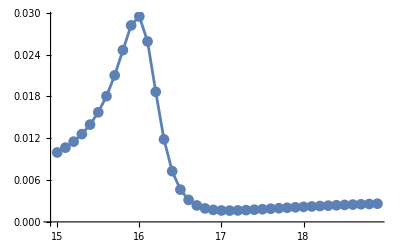

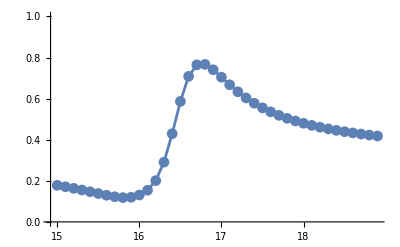

```mathematica
Clear["Global`*"]

Γ=6;Isat=16.7*3;
γ=0.00;
power=20*10^-6;
w0=650*10^-6;

I0=(2*power)/(π*w0^2);  
Ω2=Γ*√(I0/(2*Isat))
Ω1=0.4;

Ω3=Ω2*√(3/2);
Δ13=16;

ρ44=1-ρ11-ρ22-ρ33;
ρ=({{ρ11, ρ12, ρ13, ρ14}, {ρ21, ρ22, ρ23, ρ24}, {ρ31, ρ32, ρ33, ρ34}, {ρ41, ρ42, ρ43, ρ44}});
ℒ13=({{0, 0, 1, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});ℒ23=({{0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});ℒ14=({{0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});ℒz=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
Dρ[ℒ_]=ℒ.ρ.ℒ†-1/2(ℒ†.ℒ.ρ+ρ.ℒ†.ℒ);
MΓ=(1Γ)/3*Dρ[ℒ13]+(2Γ)/3*Dρ[ℒ23]+Γ*Dρ[ℒ14];(*Γ的分配取决于CG系数*)
Mγ=γ*Dρ[ℒz];

Δ={};
σ13={};
For[Δ23=15,Δ23<19,Δ23=Δ23+0.1,
H=({{0, 0, Ω1, Ω3}, {0, Δ13-Δ23, Ω2, 0}, {Ω1, Ω2, Δ13, 0}, {Ω3, 0, 0, Δ23+6.6}});
s=Solve[{({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})==-I(H.ρ-ρ.H)+MΓ+Mγ},{ρ11,ρ12,ρ13,ρ14,ρ21,ρ22,ρ23,ρ24,ρ31,ρ32,ρ33,ρ34,ρ41,ρ42,ρ43}];

AppendTo[Δ,Δ23];AppendTo[σ13,ρ13/.s[[1]]];

]

ListPlot[Transpose[{Δ,Im[σ13]}],Joined->True,PlotMarkers->Automatic,PlotRange->All]

κ=0.037;g=0.66;as=Ω1/g;
Trans=Abs[1/(I(0+g σ13/as)/(κ/2)-1)]^2;
ListPlot[Transpose[{Δ,Trans}],Joined->True,PlotMarkers->Automatic,PlotRange->{0,1}]
```

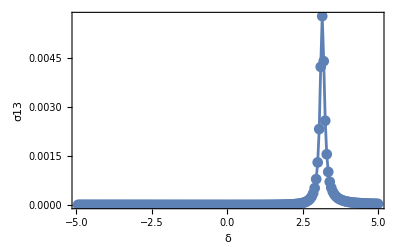

```mathematica
Clear["Global`*"]

Γ=6;
Ω1=0.4;
Ω2=30;
Ω3=Ω2*√(3/2);
Δ13=500;

ρ44=1-ρ11-ρ22-ρ33;
ρ=({{ρ11, ρ12, ρ13, ρ14}, {ρ21, ρ22, ρ23, ρ24}, {ρ31, ρ32, ρ33, ρ34}, {ρ41, ρ42, ρ43, ρ44}});
ℒ13=({{0, 0, 1, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});ℒ23=({{0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});ℒ14=({{0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});ℒ24=({{0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}});
Dρ[ℒ_]=ℒ.ρ.ℒ†-1/2(ℒ†.ℒ.ρ+ρ.ℒ†.ℒ);
MΓ=Γ/2*Dρ[ℒ13]+Γ/2*Dρ[ℒ23]+Γ/2*Dρ[ℒ14]+Γ/2*Dρ[ℒ24];(*Γ的分配取决于CG系数*)

Δ={};
σ13={};
For[Δ23=Δ13-5,Δ23<Δ13+5,Δ23=Δ23+0.05,
H=({{0, 0, Ω1, Ω1}, {0, Δ13-Δ23, Ω2, Ω2}, {Ω1, Ω2, Δ13, 0}, {Ω1, Ω2, 0, Δ13+167}});
s=Solve[{({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})==-I(H.ρ-ρ.H)+MΓ},{ρ11,ρ12,ρ13,ρ14,ρ21,ρ22,ρ23,ρ24,ρ31,ρ32,ρ33,ρ34,ρ41,ρ42,ρ43}];

AppendTo[Δ,Δ13-Δ23];AppendTo[σ13,ρ13/.s[[1]]];

]

ListPlot[Transpose[{Δ,Im[σ13]}],Joined->True,PlotMarkers->Automatic,PlotRange->All,Frame->True,FrameLabel->{"δ","σ13"}]
```

## 光子体系

光子的fock态与谐振子十分类似
1个谐振子可以处在n态上，这与 n 个处在1态上的谐振子完全不同。

### 谐振子

#### 基本性质

谐振子基态时，|ψ_0|^2 = α/(√π)Exp(-α^2 x^2)      其中，α = √(mω/ℏ)   ，1/α 称为经典禁区。
若按照高斯光的定义 Exp(-2x^2/w_0^2)，则1/α = w_0/√2
涨落：	Δx = 1/(√2)1/α = w_0/2
		Δp = ℏ/(√2)α = ℏ/w_0
满足不确定关系 ΔxΔp = ℏ/2

另外，任意本征态上的涨落：Δx =   1/α √(n+1/2)        Δp = ℏα √(n+1/2) 
即 ，随着能量的线性增加，谐振子能达到的最大位置近似满足 n+1/2  = k x^2,所以涨落是根号关系。

类比光腰出的高斯光  E=((√(2/π))/(2^j*j!*w0))^(1/2)*HermiteH[j,(√2 x)/w0]*Exp[(- x^2)/w0^2];
对比得到 1/2 α^2 = 1/w0^2,将w0换成α得
E=(α/(2^j*j!*√π))^(1/2)*HermiteH[j,αx]*Exp[-1/2 α^2 x^2];
与谐振子本征波函数完全相同。

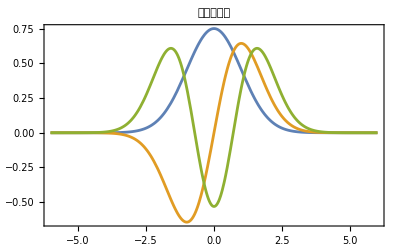

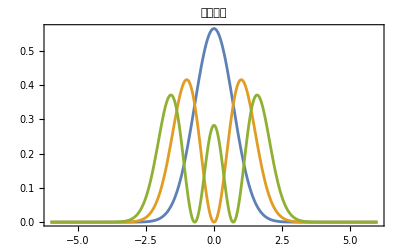

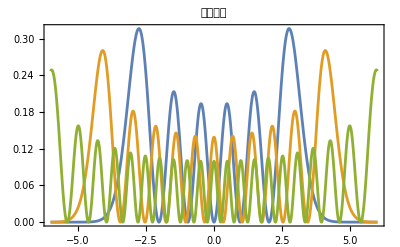

```mathematica
ℏ=1;ω=1;μ=1;
α=√((μ ω)/ℏ);
A[n_]=√(α/(√π 2^n n!));
ψ[n_,x_]=A[n]*Exp[-1/2 α^2 x^2]*HermiteH[n,α*x];
Plot[{ψ[0,x],ψ[1,x],ψ[2,x]},{x,-6,6},PlotRange->All,Frame->True,PlotLabel->"波函数图像"]
Plot[{ψ[0,x]^2,ψ[1,x]^2,ψ[2,x]^2},{x,-6,6},PlotRange->All,Frame->True,PlotLabel->"模方图像"]
Plot[{ψ[5,x]^2,ψ[10,x]^2,ψ[20,x]^2},{x,-6,6},PlotRange->All,Frame->True,PlotLabel->"模方图像"]
```

Wigner函数
-Graphics-

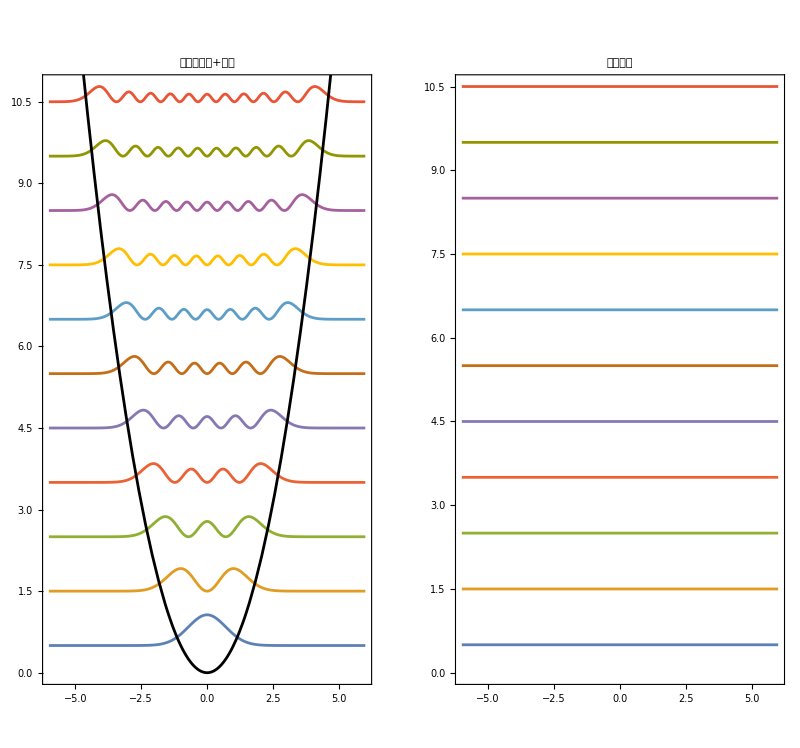

```mathematica
ℏ=1;ω=1;m=1;
α=√((m ω)/ℏ);
A[n_]=√(α/(√π 2^n n!));
ψ[n_,x_]=A[n]*Exp[-1/2 α^2 x^2]*HermiteH[n,α*x];
En[n_]=(n+1/2) ℏ ω;
eList=Table[En[i],{i,0,10}];
fList=Table[ψ[i,x]^2+En[i],{i,0,10}];
p1=Show[Plot[fList,{x,-6,6},Frame->True,AspectRatio->2,PlotLabel->"波函数模方+能量"],Plot[1/2 m ω^2 x^2,{x,-6,6},PlotStyle->Black]];
p2=Plot[eList,{x,-6,6},Frame->True,AspectRatio->2,PlotLabel->"能级分布"];
GraphicsRow[{p1,p2}]
```

#### 热态图像

-Graphics-

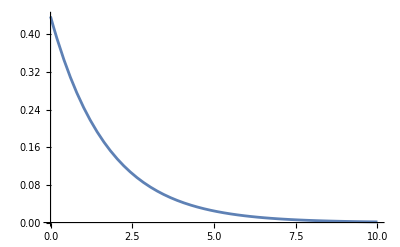

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
Import["myAtom87Rb.m"]
Import["myPhysicalParameter.m"]

A[n_]=√(1/(√π 2^n n!));
ψ[n_,x_]=A[n]*Exp[-1/2 x^2]*HermiteH[n,x];
En[n_]=n+1/2;
T=10uK;
ω=2*π*120 kHz;
c1=Sum[Exp[-((n+0.5)*ℏ*ω)/(kB*T)],{n,0,100}];
Pl[n_]=1/c1*Exp[-((n+0.5)*ℏ*ω)/(kB*T)];
nEND=10;
Plot[Pl[n],{n,0,nEND},PlotRange->All]

Eavg=Sum[Pl[n]*En[n],{n,0,nEND}];
ϕr=RandomReal[{-π,π},nEND+1];
Ψ[x_,t_]=Sum[√Pl[n]*Exp[I(En[n]t+ϕr[[n+1]])]*ψ[n,x],{n,0,nEND}];
Plot[Abs[Ψ[x,0]]^2,{x,-6,6},PlotRange->{0,1},Frame->True];
Animate[Plot[{Abs[Ψ[x,t]]^2,1/2 x^2-Eavg},{x,-6,6},PlotRange->{0,1},Frame->True],{t,0,10},AnimationRunning->False]
```

#### 相干态图像

-Graphics-
相干态的相图可以看成Wigner函数演化的轨迹，即一个半径为√2 α,粗细与谐振子基态宽度相同。

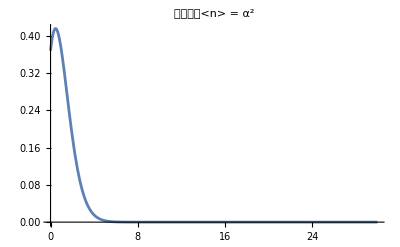

```mathematica
Clear["Global`*"]

A[n_]=√(1/(√π 2^n n!));
ψ[n_,x_]=A[n]*Exp[-1/2 x^2]*HermiteH[n,x];
En[n_]=n+1/2;
α0=1;
c[α_,n_]=Exp[-α^2/2]*α^n/(√(n!));
coh[α_,x_,t_]=Sum[c[α,n]*ψ[n,x]*Exp[I*En[n]*t],{n,0,30}];
Plot[c[α0,n]^2,{n,0,30},PlotRange->All,PlotLabel->"泊松分布<n> = α^2"]
Animate[Plot[{Abs[coh[α0,x,t]]^2,α0+0*x},{x,-6,6},PlotRange->{0,1},Frame->True,GridLines->{{-√2 α0,√2 α0}}],{t,0,6.2},AnimationRunning->False]
```

#### 压缩态

#### JCM耦合

二能级

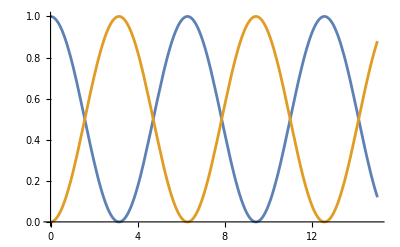

```mathematica
Clear["Global`*"]
Δ=0;
Ω=1;

dcdt=({{c1'[t]}, {c2'[t]}});
H=({{0, Ω/2}, {Ω/2, Δ}});
ct=({{c1[t]}, {c2[t]}});

s=DSolve[{dcdt==- I*H.ct,({{c1[0]}, {c2[0]}})==({{1}, {0}})},{c1[t],c2[t]},t];
Evaluate[c1[t]/.s];
Evaluate[c2[t]/.s];
Plot[{Evaluate[Abs[c1[t]]^2/.s],Evaluate[Abs[c2[t]]^2/.s]},{t,0,15},PlotRange->All]
```

谐振子

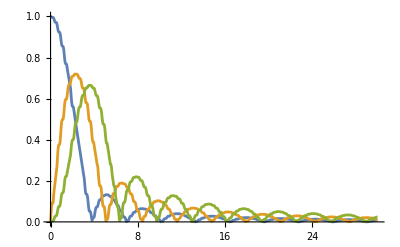

```mathematica
Clear["Global`*"]
Δ=0;
Ω=1;
ω=10;
dim=20;

dcdt=Table[{c[n]'[t]},{n,0,dim-1}];
(**)
Hct=Table[{- I(Ω Cos[ω*t]*c[n-1][t]+n*ω*c[n][t]+Ω Cos[ω*t]*c[n+1][t])},{n,1,dim-2}];
PrependTo[Hct,{- I Ω Cos[ω*t]*c[1][t]}];
AppendTo[Hct,{- I(Ω Cos[ω*t]*c[dim-2][t]+(dim-1)*ω*c[dim-1][t])}];
(**)
ct0=Table[{c[n][0]},{n,0,dim-1}];
(**)
t0c=Table[{0},{n,0,dim-2}];
PrependTo[t0c,{1}];
(**)
y=Table[c[n],{n,0,dim-1}];

s=NDSolve[{dcdt==Hct,ct0==t0c},y,{t,0,30}];
Table[a[n][t_]=First[Abs[c[n][t]]/.s],{n,0,dim-1}];

Plot[{a[0][t],a[1][t],a[2][t]},{t,0,30},PlotRange->All]
plist[t_]=Table[{n,a[n][t]},{n,0,dim-1}];

Animate[ListPlot[plist[t],Joined->True,PlotMarkers->"OpenMarkers",PlotRange->{{0,dim},{0,1}},Frame->True],{t,0,20},AnimationRunning->False]
```

### 用谐振子理解光子

谐振子：给定谐振频率ω后，不论谐振子处在哪个态上(1或者100)，谐振频率都是ω。
                    但不同态上的能量不同(E/ℏ = n+1/2)，波函数也不同。
谐振子的位置 x 可以认为对应光子的电场 ϵ 。  
电场的平均值为零(因为电场可以有正负，最后抵消(交变电场平均值为零))，但电场的涨落Δϵ 也满足类似谐振子的关系(交变电场有效值不为零)。
Δx =   1/α √(n+1/2) 
在谐振子中1/α表示基态经典禁区位置，Δx 表示谐振子可以运动到的位置。那么电场的涨落Δϵ 也可以认为是电场可以达到的最大值。谐振子  x^2 即是能量有关 ，而光子 ϵ^2 也是能量。
如果理解了为什么不同谐振子态是正交的，也就可以理解为什么不同fock态是正交的，因为其概率分布是类似三角函数的形式。而不是简单的电场越大概率越小，电场越小的概率越大那么简单。

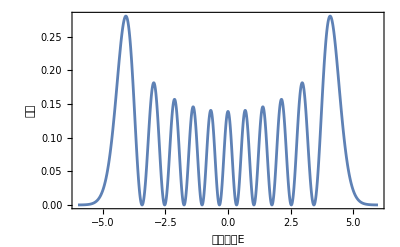

```mathematica
ℏ=1;ω=1;μ=1;
α=√((μ ω)/ℏ);
A[n_]=√(α/(√π 2^n n!));
ψ[n_,x_]=A[n]*Exp[-1/2 α^2 x^2]*HermiteH[n,α*x];
Plot[{ψ[10,x]^2},{x,-6,6},PlotRange->All,Frame->True,FrameLabel->{"电场大小E","概率"}]
```

### 经典光与量子光的关系

#### 二能级

#### 三能级

H=(0 | 0 | Ω1
0 | δ | Ω2
Ω1 | Ω2 | Δ)变成   H=(0 | 0 | g
0 | δ | Ω2
g | Ω2 | Δ)

### 光子相位

光子的fock态与谐振子十分类似
1个谐振子可以处在n态上，这与 n 个处在1态上的谐振子完全不同。
所以，在描述两个谐振子干涉时，不是态

## 光与原子耦合

### 二能级原子

#### 基础

H = ℏωa†a + ℏω_0σ†σ + ℏg (a†σ + aσ†)

若初始光子态为n，且n很大，n-1≈ n ≈ n+1，则哈密顿量可以不用考虑光子态，只考虑原子态
H = Δ↑↑+ g√n↓↑+ g√n↑↓= (0 | g √n
g √n | Δ)

若初始光子态为1
H = ℏωa†a + ℏω_0σ†σ + ℏg (a†σ + aσ†)
     = ℏω11 + ℏω_0↑↑ + ℏg (↓1↑0  +↑0↓1 )
  (0↓ | 0↑ | 1↓ | 1↑)
 = ℏ(0 | 0 | 0 | 0
0 | ω_0 | g | 0
0 | g | ω | 0
0 | 0 | 0 | ω+ω_0)
物理上认为若初态为1↓，则不可能有0↓和1↑态（能量守恒），并旋转波近似：H = (0 | g
g | Δ)

描述原子的自发辐射引入Lindblad 方程
若光子不只与原子相互作用，其自身还受到Cavity的影响，则描述光子从Cavity中的泄露也需要用到Lindblad 方程

```mathematica
ρ=({{ρ11, ρ12, ρ31, ρ41}, {ρ21, ρ22, ρ23, ρ24}, {ρ31, ρ32, ρ33, ρ34}, {ρ41, ρ42, ρ43, ρ44}});H=({{0, 0, 0, 0}, {0, Δ, g, 0}, {0, g, 0, 0}, {0, 0, 0, ω0}});
ℒ13=KroneckerProduct[({{0, 1}, {0, 0}}),({{1, 0}, {0, 1}})];
Dρ[ℒ_]=ℒ.ρ.ℒ†-1/2(ℒ†.ℒ.ρ+ρ.ℒ†.ℒ);
MΓ=Γ*Dρ[ℒ13];
MatrixForm[-I(H.ρ-ρ.H)+MΓ]
```

(Γ ρ33 | -ⅈ (-Δ ρ12-g ρ31)+Γ ρ34 | ⅈ g ρ12-(Γ ρ31)/2 | -(Γ ρ41)/2+ⅈ ρ41 ω0
-ⅈ (Δ ρ21+g ρ31)+Γ ρ43 | -ⅈ (-g ρ23+g ρ32)+Γ ρ44 | -(Γ ρ23)/2-ⅈ (-g ρ22+Δ ρ23+g ρ33) | -(Γ ρ24)/2-ⅈ (Δ ρ24+g ρ34-ρ24 ω0)
-ⅈ g ρ21-(Γ ρ31)/2 | -(Γ ρ32)/2-ⅈ (g ρ22-Δ ρ32-g ρ33) | -ⅈ (g ρ23-g ρ32)-Γ ρ33 | -Γ ρ34-ⅈ (g ρ24-ρ34 ω0)
-(Γ ρ41)/2-ⅈ ρ41 ω0 | -(Γ ρ42)/2-ⅈ (-Δ ρ42-g ρ43+ρ42 ω0) | -Γ ρ43-ⅈ (-g ρ42+ρ43 ω0) | -Γ ρ44)

```mathematica
ρ=({{ρ11, ρ12, ρ31, 0}, {ρ21, ρ22, ρ23, 0}, {ρ31, ρ32, ρ33, 0}, {0, 0, 0, 0}});H=({{0, 0, 0, 0}, {0, Δ, g, 0}, {0, g, 0, 0}, {0, 0, 0, ω0}});
ℒ13=KroneckerProduct[({{0, 1}, {0, 0}}),({{1, 0}, {0, 1}})];
Dρ[ℒ_]=ℒ.ρ.ℒ†-1/2(ℒ†.ℒ.ρ+ρ.ℒ†.ℒ);
MΓ=Γ*Dρ[ℒ13];
MatrixForm[MΓ]
MatrixForm[-I(H.ρ-ρ.H)+MΓ]
```

(Γ ρ33 | 0 | -(Γ ρ31)/2 | 0
0 | 0 | -(Γ ρ23)/2 | 0
-(Γ ρ31)/2 | -(Γ ρ32)/2 | -Γ ρ33 | 0
0 | 0 | 0 | 0)

(Γ ρ33 | -ⅈ (-Δ ρ12-g ρ31) | ⅈ g ρ12-(Γ ρ31)/2 | 0
-ⅈ (Δ ρ21+g ρ31) | -ⅈ (-g ρ23+g ρ32) | -(Γ ρ23)/2-ⅈ (-g ρ22+Δ ρ23+g ρ33) | 0
-ⅈ g ρ21-(Γ ρ31)/2 | -(Γ ρ32)/2-ⅈ (g ρ22-Δ ρ32-g ρ33) | -ⅈ (g ρ23-g ρ32)-Γ ρ33 | 0
0 | 0 | 0 | 0)

```mathematica
a=({{0, 1, 0}, {0, 0, 1}, {0, 0, 0}});
MatrixForm[a†.a]
```

(0 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Clear["Global`*"]
Δ=0;
Ω=1;

dcdt=({{c1'[t]}, {c2'[t]}});
H=({{0, Ω/2}, {Ω/2, Δ}});ct=({{c1[t]}, {c2[t]}});
ct0=({{c1[0]}, {c2[0]}});c0=({{1}, {0}});


s=DSolve[{dcdt==- I*H.ct,ct0==c0},{c1[t],c2[t]},t];
Evaluate[c1[t]/.s];
Evaluate[c2[t]/.s];
Plot[{Evaluate[Abs[c1[t]]^2/.s],Evaluate[Abs[c2[t]]^2/.s]},{t,0,15},PlotRange->All]
```

-Graphics-

#### 与腔耦合

原子的衰减时间只与Γ有关，腔的充能时间只与κ有关

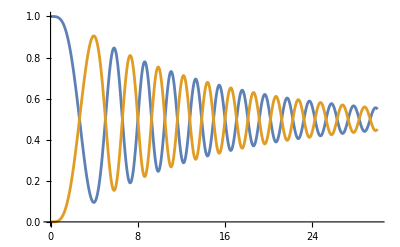

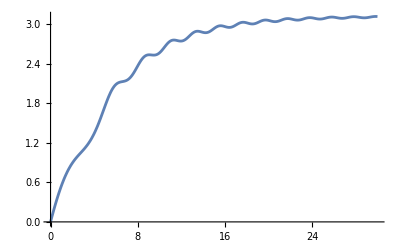

```mathematica
Clear["Global`*"]
Δ=0;
g=0.5;
κ=0.2;
ϵin=1;
Γ=0.1;
s=NDSolve[{ϵ'[t]== -κ ϵ[t]+I g ρ12[t]+√(2κ)ϵin,
ρ11'[t]==-I g ϵ[t](ρ21[t]-ρ12[t])+Γ*ρ22[t],
ρ12'[t]==-I Δ*ρ12[t]-I g ϵ[t](ρ22[t]-ρ11[t])-Γ/2*ρ12[t],
ρ21'[t]==I Δ*ρ21[t]+I g ϵ[t](ρ22[t]-ρ11[t])-Γ/2*ρ21[t],
ρ22'[t]==I g ϵ[t](ρ21[t]-ρ12[t])-Γ*ρ22[t],

ρ11[0]==1,ρ12[0]==0,ρ21[0]==0,ρ22[0]==0,ϵ[0]==0},{ρ11,ρ12,ρ21,ρ22,ϵ},{t,0,100}];
Plot[{Evaluate[Abs[ρ11[t]]/.s],Evaluate[Abs[ρ22[t]]/.s]},{t,0,30},PlotRange->All]
Plot[{Evaluate[Abs[ϵ[t]]/.s]},{t,0,30},PlotRange->All]
```

```mathematica
Clear["Global`*"]
Δ=0;
g=0.5;
κ=0.2;
ϵin=1;
Γ=0.1;

ρ=({{ρ11[t], ρ12[t]}, {ρ21[t], ρ22[t]}});H=({{0, g*ϵ[t]}, {g*ϵ[t]*, Δ}});ℒ12=({{0, 1}, {0, 0}});
Dρ[ℒ_]=ℒ.ρ.ℒ†-1/2(ℒ†.ℒ.ρ+ρ.ℒ†.ℒ);
MΓ=Γ*Dρ[ℒ12];
ρt=({{ρ11'[t], ρ12'[t]}, {ρ21'[t], ρ22'[t]}});ρt=ArrayFlatten[({{ρt, 0}, {0, ϵ'[t]}})];
ρH=-I(H.ρ-ρ.H)+MΓ;ρH=ArrayFlatten[({{ρH, 0}, {0, -κ ϵ[t]+I g ρ12[t]+√(2κ)ϵin}})];
ρ0=({{ρ11[0], ρ12[0]}, {ρ21[0], ρ22[0]}});ρ0=ArrayFlatten[({{ρ0, 0}, {0, ϵ[0]}})];
c0=({{1, 0, 0}, {0, 0, 0}, {0, 0, 0}});

s=NDSolve[{ρt==ρH,ρ0== c0},{ρ11,ρ12,ρ21,ρ22,ϵ},{t,0,30}];
Plot[{Evaluate[ρ11[t]/.s],Evaluate[ρ22[t]/.s]},{t,0,30},PlotRange->All]
Plot[{Evaluate[Abs[ϵ[t]]/.s]},{t,0,30},PlotRange->All]
```

-Graphics-

-Graphics-

### 三能级

```mathematica
Clear["Global`*"]
Δ=0;δ=0;
Ω2=5;
g=0.5;
κ=0.2;
ϵin=1;
Γ=0.1;
ℒ13=({{0, 0, 1}, {0, 0, 0}, {0, 0, 0}});ℒ23=({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}});

ρ33=1-ρ11-ρ22;
ρ=({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}});H=({{0, 0, g*ϵ}, {0, δ, Ω2/2}, {g*ϵ, Ω2/2, Δ}});
Dρ[ℒ_]=ℒ.ρ.ℒ†-1/2(ℒ†.ℒ.ρ+ρ.ℒ†.ℒ);
MΓ=(1Γ)/3*Dρ[ℒ13]+(2Γ)/3*Dρ[ℒ23];
ρt=IdentityMatrix[{4,4}]*0;
ρH=-I(H.ρ-ρ.H)+MΓ;ρH=ArrayFlatten[({{ρH, 0}, {0, -κ ϵ+I g ρ13+√(2κ)ϵin}})];
s=NSolve[{ρt==ρH},{ρ11,ρ12,ρ13,ρ21,ρ22,ρ23,ρ31,ρ32,ϵ}];
ρ13/.s
ϵ/.s
```

{-1.41421+1.26491 ⅈ,1.41421+1.26491 ⅈ,0.}

{0.-3.53553 ⅈ,0.+3.53553 ⅈ,3.16228}

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}